## Wave Equation on a Finite Interval: D-D BCs.

```mathematica
Manipulate[Plot[Cos[2*Pi*t]*Sin[2*Pi*x],{x,0,1},PlotRange->{-1,1}],{t,0,2}]
```

```mathematica
Manipulate[Plot[(Cos[3*Pi*t]-Sin[3*Pi*t])*Sin[3*Pi*x],{x,0,1},PlotRange->{-1.5,1.5}],{t,0,2}]
```

```mathematica
Manipulate[Plot[Cos[Pi*t]*Sin[Pi*x]+Sin[2*Pi*t]*Sin[2*Pi*x],{x,0,1},PlotRange->{-2,2}],{t,0,2}]
```

## Wave Equation on a Finite Interval: N-N BCs.

```mathematica
Manipulate[Plot[Cos[3*Pi*t]*Cos[3*Pi*x],{x,0,1},PlotRange->{-1,1}],{t,0,2}]
```

```mathematica
Manipulate[Plot[6+5*Sin[Pi*t]*Cos[Pi*x]-Cos[4*Pi*t]*Cos[4*Pi*x],{x,0,1},PlotRange->{0,12}],{t,0,2}]
```

## Wave Equation on a Finite Interval: D-N BCs.

```mathematica
Manipulate[Plot[Cos[0.5*Pi*t]*Sin[0.5*Pi*x],{x,0,1},PlotRange->{-1,1}],{t,0,4}]
```

```mathematica
Manipulate[Plot[Cos[0.5*Pi*t]*Sin[0.5*Pi*x]-Sin[3.5*Pi*t]*Sin[3.5*Pi*x],{x,0,1},PlotRange->{-2,2}],{t,0,4}]
```

## Wave Equation on a Finite Interval: Periodic BCs.

```mathematica
Manipulate[Plot[Sin[2*Pi*t]*Cos[2*Pi*x],{x,0,1},PlotRange->{-1,1}],{t,0,1}]
```

```mathematica
Manipulate[Plot[Sin[2*Pi*t]*Sin[2*Pi*x],{x,0,1},PlotRange->{-1,1}],{t,0,1}]
```

```mathematica
Manipulate[Plot[Sin[2*Pi*t]*(Cos[2*Pi*x]+Sin[2*Pi*x]),{x,0,1},PlotRange->{-2,2}],{t,0,1}]
```

```mathematica
Manipulate[Plot[Sin[2*Pi*t]*Cos[2*Pi*x]+Cos[6*Pi*t]*Sin[6*Pi*x]-Sin[12*Pi*t]*Sin[12*Pi*x],{x,0,1},PlotRange->{-2.5,2.5}],{t,0,1}]
```

## Quasiperiodic (multiplier -1):

```mathematica
Manipulate[Plot[Cos[0.5*3*Pi*t]*Cos[3*Pi*x],{x,0,1},PlotRange->{-1,1}],{t,0,4}]
```

```mathematica
Manipulate[Plot[Cos[0.5*3*Pi*t]*Sin[3*Pi*x],{x,0,1},PlotRange->{-1,1}],{t,0,4}]
```

```mathematica
Manipulate[Plot[0.5*Cos[0.5*3*Pi*t]*Cos[3*Pi*x]+0.5*Sin[0.5*7*Pi*t]*Sin[7*Pi*x],{x,0,1},PlotRange->{-1,1}],{t,0,4}]
```

```mathematica
Manipulate[Plot[∑_(n=0)^∞ (1/n!)*Cos[0.5*(2*n+1)*Pi*t]*Cos[(2*n+1)*Pi*x],{x,0,1},PlotRange->{-5,5}],{t,0,4}]
```

```mathematica
qsol[x_,t_]=∑_(n=0)^∞ (1/n!)*Cos[0.5*(2*n+1)*Pi*t]*Cos[(2*n+1)*Pi*x]
```

0.25 ⅇ^((0.-1.5708 ⅈ) t-ⅈ π x) (1. 2.71828^(2.71828^((0.-3.14159 ⅈ) t-(0.+6.28319 ⅈ) x))+1. 2.71828^(2.71828^((0.+3.14159 ⅈ) t-(0.+6.28319 ⅈ) x)) ⅇ^((0.+3.14159 ⅈ) t)+1. 2.71828^(2.71828^((0.-3.14159 ⅈ) t+(0.+6.28319 ⅈ) x)) ⅇ^(2 ⅈ π x)+1. 2.71828^(2.71828^((0.+3.14159 ⅈ) t+(0.+6.28319 ⅈ) x)) ⅇ^((0.+3.14159 ⅈ) t+2 ⅈ π x))

```mathematica
Manipulate[Plot[qsol[x,t],{x,0,1},PlotRange->{-5,5}],{t,0,4}]
```

```mathematica
qsol2[x_,t_]=∑_(n=0)^∞ ((-1)^n/n!)*Cos[0.5*(2*n+1)*Pi*t]*Cos[(2*n+1)*Pi*x]
```

0.25 2.71828^(-1. 2.71828^((0.-3.14159 ⅈ) t-(0.+6.28319 ⅈ) x)-1. 2.71828^((0.+3.14159 ⅈ) t-(0.+6.28319 ⅈ) x)-1. 2.71828^((0.-3.14159 ⅈ) t+(0.+6.28319 ⅈ) x)-1. 2.71828^((0.+3.14159 ⅈ) t+(0.+6.28319 ⅈ) x)) ⅇ^((0.-1.5708 ⅈ) t-ⅈ π x) (1. 2.71828^(1. 2.71828^((0.+3.14159 ⅈ) t-(0.+6.28319 ⅈ) x)+1. 2.71828^((0.-3.14159 ⅈ) t+(0.+6.28319 ⅈ) x)+1. 2.71828^((0.+3.14159 ⅈ) t+(0.+6.28319 ⅈ) x))+1. 2.71828^(1. 2.71828^((0.-3.14159 ⅈ) t-(0.+6.28319 ⅈ) x)+1. 2.71828^((0.-3.14159 ⅈ) t+(0.+6.28319 ⅈ) x)+1. 2.71828^((0.+3.14159 ⅈ) t+(0.+6.28319 ⅈ) x)) ⅇ^((0.+3.14159 ⅈ) t)+1. 2.71828^(1. 2.71828^((0.-3.14159 ⅈ) t-(0.+6.28319 ⅈ) x)+1. 2.71828^((0.+3.14159 ⅈ) t-(0.+6.28319 ⅈ) x)+1. 2.71828^((0.+3.14159 ⅈ) t+(0.+6.28319 ⅈ) x)) ⅇ^(2 ⅈ π x)+1. 2.71828^(1. 2.71828^((0.-3.14159 ⅈ) t-(0.+6.28319 ⅈ) x)+1. 2.71828^((0.+3.14159 ⅈ) t-(0.+6.28319 ⅈ) x)+1. 2.71828^((0.-3.14159 ⅈ) t+(0.+6.28319 ⅈ) x)) ⅇ^((0.+3.14159 ⅈ) t+2 ⅈ π x))

```mathematica
Manipulate[Plot[qsol2[x,t],{x,0,1},PlotRange->{-2,2}],{t,0,4}]
```

```mathematica
qsol3[x_,t_]=∑_(n=1)^∞ ((-1)^n/n)*Cos[0.5*(2*n+1)*Pi*t]*Cos[(2*n+1)*Pi*x]
```

-0.25 ⅇ^((0.-1.5708 ⅈ) t-ⅈ π x) (1. ⅇ^((0.+3.14159 ⅈ) t+2 ⅈ π x) Log[1.+2.71828^((0.+3.14159 ⅈ) t+(0.+6.28319 ⅈ) x)]+1. Log[1. 2.71828^((0.-3.14159 ⅈ) t-(0.+6.28319 ⅈ) x) (1.+1. 2.71828^((0.+3.14159 ⅈ) t+(0.+6.28319 ⅈ) x))]+1. ⅇ^(2 ⅈ π x) Log[2.71828^((0.-3.14159 ⅈ) t) (1. 2.71828^((0.+3.14159 ⅈ) t)+2.71828^((0.+6.28319 ⅈ) x))]+1. ⅇ^((0.+3.14159 ⅈ) t) Log[1. 2.71828^((0.-6.28319 ⅈ) x) (1. 2.71828^((0.+3.14159 ⅈ) t)+1. 2.71828^((0.+6.28319 ⅈ) x))])

```mathematica
Manipulate[Plot[qsol3[x,t],{x,0,1},PlotRange->{-2,2}],{t,0,4}]
```

```mathematica
qsol4[x_,t_]=∑_(n=1)^∞ (1/n^2)*Cos[0.5*(2*n+1)*Pi*t]*(0.25*Cos[(2*n+1)*Pi*x]-0.75*Sin[(2*n+1)*Pi*x])
```

(0.1875+0.0625 ⅈ) 2.71828^((0.-1.5708 ⅈ) t-(0.+3.14159 ⅈ) x) ((0.-1. ⅈ) PolyLog[2.,2.71828^((0.-3.14159 ⅈ) t-(0.+6.28319 ⅈ) x)]-(0.+1. ⅈ) 2.71828^((0.+3.14159 ⅈ) t) PolyLog[2.,2.71828^((0.+3.14159 ⅈ) t-(0.+6.28319 ⅈ) x)]+(0.6+0.8 ⅈ) 2.71828^((0.+6.28319 ⅈ) x) PolyLog[2.,2.71828^((0.-3.14159 ⅈ) t+(0.+6.28319 ⅈ) x)]+(0.6+0.8 ⅈ) 2.71828^((0.+3.14159 ⅈ) t+(0.+6.28319 ⅈ) x) PolyLog[2.,2.71828^((0.+3.14159 ⅈ) t+(0.+6.28319 ⅈ) x)])

```mathematica
Manipulate[Plot[qsol4[x,t],{x,0,1},PlotRange->{-2,2}],{t,0,4}]
```

## Exploring Robin BCs:

Let’s explore the possible space of eigenvalues. First, when we look for positive eigenvalues, we will want to solve the following equation:

```mathematica
Tan[s]==((a+b)*s)/(s^2-a*b)
```

Tan[s]==((a+b) s)/(-a b+s^2)

We’ll plot both sides of this and look for intersections (note that we require s>0):

```mathematica
Manipulate[Plot[{Tan[s],((a+b)*s)/(s^2-a*b)},{s,0,10},PlotRange->{-20,20}],{a,-10,10},{b,-10,10}]
```

Let’s explicitly consider the following three cases and just manipulate b: a=-1, a=0, a=1:

```mathematica
Manipulate[Plot[{Tan[s],((b-1)*s)/(s^2+b)},{s,0,10},PlotRange->{0,20}],{b,-10,10}]
```

```mathematica
Manipulate[Plot[{Tan[s],b/s},{s,0,10},PlotRange->{0,20}],{b,0,10}]
```

```mathematica
Manipulate[Plot[{Tan[s],((b+1)*s)/(s^2-b)},{s,0,10},PlotRange->{0,2}],{b,-1,2}]
```

We can also break the problem up into some sample cases:

```mathematica
Manipulate[Plot[{Tan[s],((a+b)*s)/(s^2-a*b)},{s,0,10},PlotRange->{-10,10},GridLines->{{Pi/2,3*Pi/2,5*Pi/2,7*Pi/2},None},Ticks->{{Pi/2,Pi,3*Pi/2,2Pi,5*Pi/2,3Pi,7*Pi/2},Automatic},PlotLabel->"α , β > 0"],{a,0,10},{b,0,10}]
```

```mathematica
Manipulate[Plot[{Tan[s],((a+b)*s)/(s^2-a*b)},{s,0,3Pi},PlotRange->{0,5},GridLines->{{Pi/2,3*Pi/2,5*Pi/2,7*Pi/2},None},Ticks->{{Pi/2,Pi,3*Pi/2,2Pi,5*Pi/2,3Pi,7*Pi/2},Automatic},PlotLabel->"α < 0 , β > 0 , α + β > 0"],{a,-b+0.0001,0},{b,0.1,20}]
```

```mathematica
Manipulate[Plot[{Tan[s],((a+b)*s)/(s^2-a*b)},{s,0,3Pi},PlotRange->{-10,0},GridLines->{{Pi/2,3*Pi/2,5*Pi/2,7*Pi/2},None},Ticks->{{Pi/2,Pi,3*Pi/2,2Pi,5*Pi/2,3Pi,7*Pi/2},Automatic},PlotLabel->"α < 0 , β > 0 , α + β < 0"],{a,-20,-2},{b,0.1,-a-0.001}]
```

Next, when we look for negative eigenvalues, we will want to solve the following equation:

```mathematica
Tanh[s]==-((a+b)*s)/(s^2+a*b)
```

Tanh[s]==-((a+b) s)/(a b+s^2)

Plot these against each other again:

```mathematica
Manipulate[Plot[{Tanh[s],-((a+b)*s)/(s^2+a*b)},{s,0,30},PlotRange->{0,2}],{a,-20,7},{b,-10,10}]
```

Again let’s just manipulate b, taking a=-5,0,5:

```mathematica
Manipulate[Plot[{Tanh[s],-((b-5)*s)/(s^2-5*b)},{s,0,11},PlotRange->{0,2},PlotLabel->"α = 5"],{b,-10,10}]
```

```mathematica
Manipulate[Plot[{Tanh[s],-b/s},{s,0,11},PlotRange->{0,2}],{b,-10,10}]
```

```mathematica
Manipulate[Plot[{Tanh[s],-((5+b)*s)/(s^2+5*b)},{s,0,11},PlotRange->{0,2},PlotLabel->"α = -5"],{b,-10,10}]
```

Some sample plots:

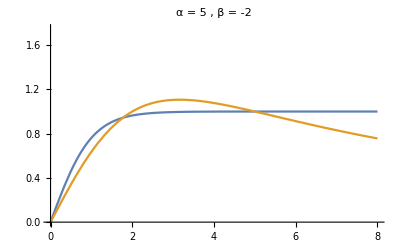

```mathematica
Plot[{Tanh[s],-((-2-5)*s)/(s^2-5*(-2))},{s,0,8},PlotRange->{0,1.75},PlotLabel->"α = 5 , β = -2"]
```

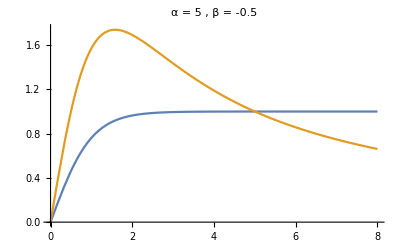

```mathematica
Plot[{Tanh[s],-((-0.5-5)*s)/(s^2-5*(-0.5))},{s,0,8},PlotRange->{0,1.75},PlotLabel->"α = 5 , β = -0.5"]
```

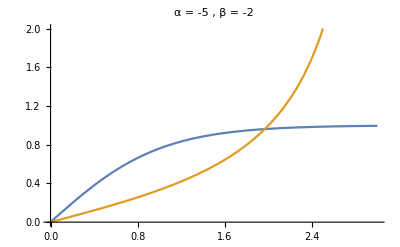

```mathematica
Plot[{Tanh[s],-((5-2)*s)/(s^2+5*(-2))},{s,0,3},PlotRange->{0,2},PlotLabel->"α = -5 , β = -2"]
```

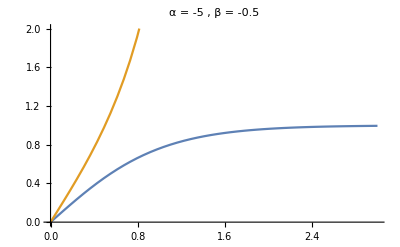

```mathematica
Plot[{Tanh[s],-((5-0.5)*s)/(s^2+5*(-0.5))},{s,0,3},PlotRange->{0,2},PlotLabel->"α = -5 , β = -0.5"]
```

Let’s now do Dirichlet at the left end of the interval, and Robin at the right. Looking for a negative eigenvalue involves solving the equation:

```mathematica
s==-b*Tanh[s]
```

s==-b Tanh[s]

Plot both of these and look for intersections where s>0:

```mathematica
Manipulate[Plot[{s,-b*Tanh[s]},{s,0,11},PlotRange->{-10,10}],{b,-10,10}]
```

```mathematica
Manipulate[Plot[{s,-b*Tanh[s]},{s,0,0.5},PlotRange->{0,0.5}],{b,-1.1,-0.9}]
```

Let’s take a look at three representative values of b:

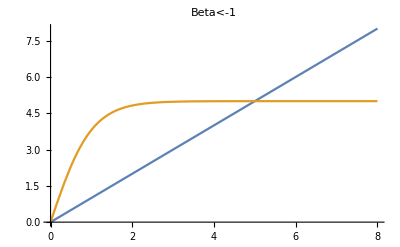

```mathematica
Plot[{s,5*Tanh[s]},{s,0,8},PlotRange->{0,8},PlotLabel->"Beta<-1"]
```

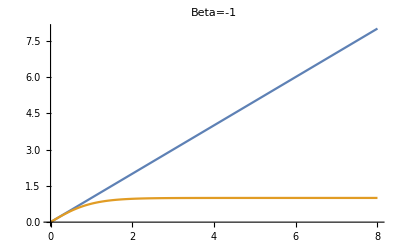

```mathematica
Plot[{s,Tanh[s]},{s,0,8},PlotRange->{0,8},PlotLabel->"Beta=-1"]
```

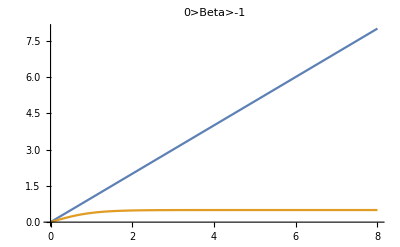

```mathematica
Plot[{s,0.5*Tanh[s]},{s,0,8},PlotRange->{0,8},PlotLabel->"0>Beta>-1"]
```

Looking at Dirichlet BC on one end, Robin on the other, trying to find e-vals:

```mathematica
Manipulate[Plot[{s,-b*Tan[s]},{s,0,7*Pi/2},PlotRange->{0,7*Pi/2},Ticks->{{0,Pi,2Pi,3Pi},Automatic},GridLines->{{Pi/2,Pi,3*Pi/2,2*Pi,5*Pi/2,3*Pi,7*Pi/2},None}],{b,-2,2}]
```

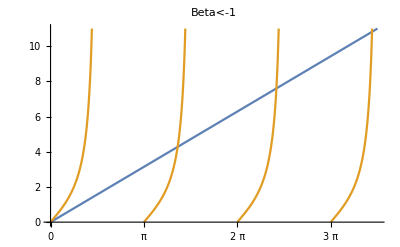

```mathematica
Plot[{s,2*Tan[s]},{s,0,7*Pi/2},PlotRange->{0,7*Pi/2},Ticks->{{0,Pi,2Pi,3Pi},Automatic},GridLines->{{Pi/2,Pi,3*Pi/2,2*Pi,5*Pi/2,3*Pi,7*Pi/2},None},PlotLabel->"Beta<-1"]
```

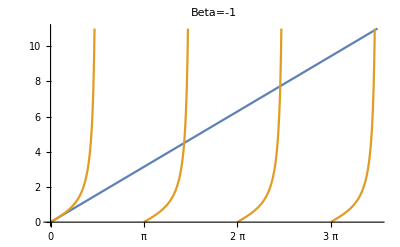

```mathematica
Plot[{s,Tan[s]},{s,0,7*Pi/2},PlotRange->{0,7*Pi/2},Ticks->{{0,Pi,2Pi,3Pi},Automatic},GridLines->{{Pi/2,Pi,3*Pi/2,2*Pi,5*Pi/2,3*Pi,7*Pi/2},None},PlotLabel->"Beta=-1"]
```

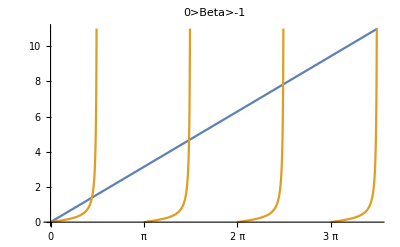

```mathematica
Plot[{s,0.25*Tan[s]},{s,0,7*Pi/2},PlotRange->{0,7*Pi/2},Ticks->{{0,Pi,2Pi,3Pi},Automatic},GridLines->{{Pi/2,Pi,3*Pi/2,2*Pi,5*Pi/2,3*Pi,7*Pi/2},None},PlotLabel->"0>Beta>-1"]
```

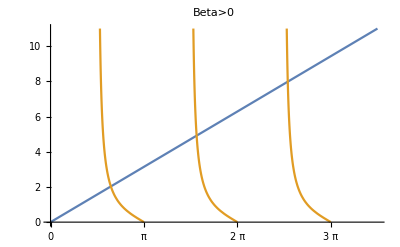

```mathematica
Plot[{s,-Tan[s]},{s,0,7*Pi/2},PlotRange->{0,7*Pi/2},Ticks->{{0,Pi,2Pi,3Pi},Automatic},GridLines->{{Pi/2,Pi,3*Pi/2,2*Pi,5*Pi/2,3*Pi,7*Pi/2},None},PlotLabel->"Beta>0"]
```